```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
f[x__]:=Log[PDF[MultinormalDistribution[{5,5},{{1.5,0.25},{0.25,1.5}}],{x}]][[1]]
fDerivative[f_,z_]:=Module[{x,v},v=Array[x,Length[z]];
D[f@@v,{v}]/.Thread[v->z]]
fLeapFrogStep[θ_,m_,ϵ_,logP_]:=Module[{grad,x,θ1,m1,grad1},grad=fDerivative[logP,θ];m1=m+0.5 ϵ grad; θ1=θ+ϵ m1;grad1=fDerivative[logP,θ1];m1=m1+0.5 ϵ grad1;{θ1,m1}]
fBuildTree[θ_,m_,u_,v_,j_,ϵ_,logP_,Δ_]:=Module[{Cprimed,Cprimedprimed,sprimed,sprimedprimed,res,thetaMinus,thetaPlus,mMinus,mPlus,temp1,temp2},If[j==0,res=fLeapFrogStep[θ,m,v ϵ,logP];Cprimed=If[Log[u]≤(logP[res[[1]]]-0.5 m.m),res,{res[[1]],res[[2]],{}}];sprimed=If[Log[u]<(Δ+logP[res[[1]]]-0.5 m.m),1,0]; {res[[1]],res[[2]],res[[1]],res[[2]],Cprimed,sprimed},{thetaMinus,mMinus,thetaPlus,mPlus,Cprimed,sprimed}=fBuildTree[θ,m,u,v,j-1,ϵ,logP,Δ];If[v==-1,{thetaMinus,mMinus,temp1,temp2,Cprimedprimed,sprimedprimed}=fBuildTree[thetaMinus,mMinus,u,v,j-1,ϵ,logP,Δ],
{temp1,temp2,thetaPlus,mPlus,Cprimedprimed,sprimedprimed}=fBuildTree[thetaPlus,mMinus,u,v,j-1,ϵ,logP,Δ]];sprimed=sprimed sprimedprimed If[(thetaPlus-thetaMinus).mMinus ≥ 0,1,0]If[(thetaPlus-thetaMinus).mPlus ≥ 0,1,0];Cprimed = DeleteCases[Union[{Cprimed},{Cprimedprimed}],{}]; {thetaMinus,mMinus,thetaPlus,mPlus,Cprimed,sprimed}]]
fNUTSstep[θ_,ϵ_,logP_,Δ_]:=Module[{thetaMinus=θ,thetaPlus=θ,mMinus,mPlus,j=0,C,s=1,m,temp1,temp2,Cprimed,sprimed,u,v},m=RandomVariate[MultinormalDistribution[ConstantArray[0,Length@θ],IdentityMatrix[Length@θ]],{1}][[1]];u=RandomVariate[UniformDistribution[{0,Exp[logP[θ]-0.5 m.m]}],1][[1]];
mMinus=m;mPlus=m;C={θ,m};While[s==1,v=RandomChoice[{-1,1}];If[v==-1,{thetaMinus,mMinus,temp1,temp2,Cprimed,sprimed}=fBuildTree[thetaMinus,mMinus,u,v,j,ϵ,logP,Δ],{temp1,temp2,thetaPlus,mPlus,Cprimed,sprimed}=fBuildTree[thetaPlus,mPlus,u,v,j,ϵ,logP,Δ]];
If[sprimed==1,C=Union[{C},{Cprimed}]];
s=sprimed If[(thetaPlus-thetaMinus).mMinus ≥ 0,1,0]If[(thetaPlus-thetaMinus).mPlus ≥ 0,1,0];j = j + 1];C]
fNUTSstepExtract[c_]:=Module[{dep=Depth@c},RandomChoice@DeleteCases[Flatten[c,dep-4],{}]]
fNUTSstepComplete[θ_,ϵ_,logP_,Δ_]:=Module[{c=fNUTSstep[θ,ϵ,logP,Δ]},fNUTSstepExtract[c]]
fNUTS[M_Integer,θ0_,ϵ_,logP_,Δ_]:=NestList[fNUTSstepComplete[#[[1]],ϵ,logP,Δ]&,{θ0,{}},M]
```

```mathematica
samples=fNUTS[50,{0,0},0.1,f,1000];
```

Flatten::flev: The level argument -1 in position 2 of Flatten[{{-18.3318,46.3901},{1.08461,-1.36212}},-1] should be a non-negative integer or Infinity giving the levels to flatten through or a list of lists of levels to flatten together.

RandomChoice::lrwl: The items for choice Flatten[{{-18.3318,46.3901},{1.08461,-1.36212}},-1] should be a list or a rule weights -> choices.

Flatten::flev: The level argument -1 in position 2 of Flatten[{{-18.3318,46.3901},{1.08461,-1.36212}},-1] should be a non-negative integer or Infinity giving the levels to flatten through or a list of lists of levels to flatten together.

Flatten::flev: The level argument -1. in position 2 of Flatten[{{-18.3318,46.3901},{1.08461,-1.36212}},-1.] should be a non-negative integer or Infinity giving the levels to flatten through or a list of lists of levels to flatten together.

General::stop: Further output of Flatten::flev will be suppressed during this calculation.

RandomVariate::unifr: -- Message text not found -- (UniformDistribution[{0,ⅇ^(-0.918201+PDF[MultinormalDistribution[{5,5},{{«2»},{«2»}}],{Flatten[{«2»},-1]}])}])

Part::partd: Part specification (-0.880788)⟦1⟧ is longer than depth of object.

RandomVariate::unifr: -- Message text not found -- (UniformDistribution[{0,ⅇ^(-0.418222+PDF[MultinormalDistribution[{5,5},{{«2»},{«2»}}],{(-0.880788)⟦1⟧}])}])

RandomChoice::lrwl: The items for choice Flatten[{(-0.880788)⟦1⟧,{-0.91286,0.055955}},-1] should be a list or a rule weights -> choices.

RandomVariate::unifr: -- Message text not found -- (UniformDistribution[{0,ⅇ^(-2.75844+PDF[MultinormalDistribution[{5,5},{{«2»},{«2»}}],{Flatten[{«2»},-1]}])}])

General::stop: Further output of RandomVariate::unifr will be suppressed during this calculation.

Part::partd: Part specification (-0.391105)⟦1⟧ is longer than depth of object.

RandomChoice::lrwl: The items for choice Flatten[{(-0.391105)⟦1⟧,{0.852104,0.507576}},-1] should be a list or a rule weights -> choices.

General::stop: Further output of RandomChoice::lrwl will be suppressed during this calculation.

Part::partd: Part specification 0.188334⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

IdentityMatrix::dims: Dimension specification 0 should be a positive machine integer or a pair of positive machine integers.

MultinormalDistribution::posdefprm: The value IdentityMatrix[0] at position 2 in MultinormalDistribution[{},IdentityMatrix[0]] is expected to be a symmetric positive definite matrix.

IdentityMatrix::dims: Dimension specification 0. should be a positive machine integer or a pair of positive machine integers.

General::stop: Further output of IdentityMatrix::dims will be suppressed during this calculation.

```mathematica
ListLinePlot[samples[[All,1]]]
```

Part::partd: Part specification {{{0,0},{}},{{-21.7973,12.0212},{-1.08445,0.598072},{}},{{1.51525,13.8222},{-1.03612,-0.0800439}},{{9.92394,1.22753},{-1.31101,2.01195}},{{1.93631,-2.83027},{-1.6995,-0.863361},{}},«41»,{2.07478,0.721826},2.07478,RandomChoice[Flatten[{2.07478⟦1⟧,{0.25953,0.0549713}},-1]],-0.590667,«1»}⟦All,1⟧ is longer than depth of object.

Flatten::flev: The level argument -1. in position 2 of Flatten[{{-18.3318,46.3901},{1.08461,-1.36212}},-1.] should be a non-negative integer or Infinity giving the levels to flatten through or a list of lists of levels to flatten together.

RandomChoice::lrwl: The items for choice Flatten[{{-18.3318,46.3901},{1.08461,-1.36212}},-1.] should be a list or a rule weights -> choices.

Flatten::flev: The level argument -1. in position 2 of Flatten[{(-0.880788)⟦1⟧,{-0.91286,0.055955}},-1.] should be a non-negative integer or Infinity giving the levels to flatten through or a list of lists of levels to flatten together.

RandomChoice::lrwl: The items for choice Flatten[{(-0.880788)⟦1⟧,{-0.91286,0.055955}},-1.] should be a list or a rule weights -> choices.

Flatten::flev: The level argument -1. in position 2 of Flatten[{(-0.391105)⟦1⟧,{0.852104,0.507576}},-1.] should be a non-negative integer or Infinity giving the levels to flatten through or a list of lists of levels to flatten together.

General::stop: Further output of Flatten::flev will be suppressed during this calculation.

RandomChoice::lrwl: The items for choice Flatten[{(-0.391105)⟦1⟧,{0.852104,0.507576}},-1.] should be a list or a rule weights -> choices.

General::stop: Further output of RandomChoice::lrwl will be suppressed during this calculation.

Part::partd: Part specification {{{0,0},{}},{{-21.7973,12.0212},{-1.08445,0.598072},{}},{{1.51525,13.8222},{-1.03612,-0.0800439}},{{9.92394,1.22753},{-1.31101,2.01195}},{{1.93631,-2.83027},{-1.6995,-0.863361},{}},«41»,{2.07478,0.721826},2.07478,RandomChoice[Flatten[{2.07478⟦1⟧,{0.25953,0.0549713}},-1.]],-0.590667,«1»}⟦All,1⟧ is longer than depth of object.

Part::partd: Part specification {{{0.,0.},{}},{{-21.7973,12.0212},{-1.08445,0.598072},{}},{{1.51525,13.8222},{-1.03612,-0.0800439}},{{9.92394,1.22753},{-1.31101,2.01195}},{{1.93631,-2.83027},{-1.6995,-0.863361},{}},«41»,{2.07478,0.721826},2.07478,RandomChoice[Flatten[{2.07478⟦1⟧,{0.25953,0.0549713}},-1.]],-0.590667,«1»}⟦All,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ListLinePlot::lpn: {{{0.,0.},{}},{{-21.7973,12.0212},{-1.08445,0.598072},{}},{{1.51525,13.8222},{-1.03612,-0.0800439}},{{9.92394,1.22753},{-1.31101,2.01195}},{{1.93631,-2.83027},{-1.6995,-0.863361},{}},«41»,{2.07478,0.721826},2.07478,RandomChoice[Flatten[{2.07478⟦1⟧,{0.25953,0.0549713}},-1.]],-0.590667,«1»}⟦All,1⟧ is not a list of numbers or pairs of numbers.

ListLinePlot[{{{0,0},{}},{{-21.7973,12.0212},{-1.08445,0.598072},{}},{{1.51525,13.8222},{-1.03612,-0.0800439}},{{9.92394,1.22753},{-1.31101,2.01195}},{{1.93631,-2.83027},{-1.6995,-0.863361},{}},{{23.3751,19.4906},{0.428613,0.446708},{}},{{23.1941,19.2516},{0.301668,0.39834}},{{-18.3318,46.3901},{-0.607103,0.396762},{}},RandomChoice[Flatten[{{-18.3318,46.3901},{1.08461,-1.36212}},-1]],-0.880788,RandomChoice[Flatten[{(-0.880788)⟦1⟧,{-0.91286,0.055955}},-1]],-0.391105,RandomChoice[Flatten[{(-0.391105)⟦1⟧,{0.852104,0.507576}},-1]],0.188334,RandomChoice[Flatten[{0.188334⟦1⟧,{1.02528,-1.59636}},-1]],0.233959,RandomChoice[Flatten[{0.233959⟦1⟧,{0.16978,0.297295}},-1]],Flatten[{0.233959⟦1⟧,{0.16978,0.297295}},-1],{0.233959⟦1⟧,{0.16978,0.297295}},RandomChoice[Flatten[{0.233959⟦1⟧,{-0.065092,-1.08562}},-1]],Flatten[{0.233959⟦1⟧,{-0.065092,-1.08562}},-1],{0.233959⟦1⟧,{-0.065092,-1.08562}},RandomChoice[Flatten[{0.233959⟦1⟧,{-2.03092,-1.26943}},-1]],0.465189,RandomChoice[Flatten[{0.465189⟦1⟧,{0.268174,1.3222}},-1]],0.822249,RandomChoice[Flatten[{0.822249⟦1⟧,{1.24346,0.337488}},-1]],-0.428293,RandomChoice[Flatten[{(-0.428293)⟦1⟧,{-1.113,-0.0912727}},-1]],Flatten[{(-0.428293)⟦1⟧,{-1.113,-0.0912727}},-1],{(-0.428293)⟦1⟧,{-1.113,-0.0912727}},RandomChoice[Flatten[{(-0.428293)⟦1⟧,{1.33019,-0.170378}},-1]],1.35399,RandomChoice[Flatten[{1.35399⟦1⟧,{0.32723,0.525242}},-1]],1.17298,RandomChoice[Flatten[{1.17298⟦1⟧,{-2.42802,-0.653645}},-1]],1.84536,RandomChoice[Flatten[{1.84536⟦1⟧,{-0.357429,0.867729}},-1]],-0.394,RandomChoice[Flatten[{(-0.394)⟦1⟧,{0.21317,0.845133}},-1]],Flatten[{(-0.394)⟦1⟧,{0.21317,0.845133}},-1],{(-0.394)⟦1⟧,{0.21317,0.845133}},RandomChoice[Flatten[{(-0.394)⟦1⟧,{0.763492,0.436019}},-1]],1.42651,RandomChoice[Flatten[{1.42651⟦1⟧,{-0.704246,1.14962}},-1]],Flatten[{1.42651⟦1⟧,{-0.704246,1.14962}},-1],{2.07478,0.721826},2.07478,RandomChoice[Flatten[{2.07478⟦1⟧,{0.25953,0.0549713}},-1]],-0.590667,RandomChoice[Flatten[{(-0.590667)⟦1⟧,{-0.0534429,-1.54315}},-1]]}⟦All,1⟧]

## Visualising tree

```mathematica
fNUTSstepSingle[θ_,ϵ_,logP_,Δ_]:=Module[{thetaMinus=θ,thetaPlus=θ,mMinus,mPlus,j=0,C,s=1,m,temp1,temp2,Cprimed,sprimed,u,v},m=RandomVariate[MultinormalDistribution[ConstantArray[0,Length@θ],IdentityMatrix[Length@θ]],{1}][[1]];u=RandomVariate[UniformDistribution[{0,Exp[logP[θ]-0.5 m.m]}],1][[1]];
mMinus=m;mPlus=m;C={θ,m};v=RandomChoice[{-1,1}];If[v==-1,{thetaMinus,mMinus,temp1,temp2,Cprimed,sprimed}=fBuildTree[thetaMinus,mMinus,u,v,j,ϵ,logP,Δ],{temp1,temp2,thetaPlus,mPlus,Cprimed,sprimed}=fBuildTree[thetaPlus,mPlus,u,v,j,ϵ,logP,Δ]];
If[sprimed==1,C=Union[{C},{Cprimed}]];
s=sprimed If[(thetaPlus-thetaMinus).mMinus ≥ 0,1,0]If[(thetaPlus-thetaMinus).mPlus ≥ 0,1,0];j = j + 1;C]
fNUTSstepSingleString[thetaMinus_,mMinus_,thetaPlus_,mPlus_,C_,j_,s_,u_,ϵ_,logP_,Δ_]:=Module[{thetaMinus1=thetaMinus,mMinus1=mMinus,thetaPlus1=thetaPlus,mPlus1=mPlus,s1=s,temp1,temp2,Cprimed,sprimed,v,C1,j1,dep},
v=RandomChoice[{-1,1}];If[v==-1,{thetaMinus1,mMinus1,temp1,temp2,Cprimed,sprimed}=fBuildTree[thetaMinus1,mMinus1,u,v,j,ϵ,logP,Δ],{temp1,temp2,thetaPlus1,mPlus1,Cprimed,sprimed}=fBuildTree[thetaPlus1,mPlus,u,v,j,ϵ,logP,Δ]];
dep=Depth@Cprimed-4;
If[sprimed==1,C1=Join[{C},{Cprimed}]];
s1=sprimed If[(thetaPlus1-thetaMinus1).mMinus1 ≥ 0,1,0]If[(thetaPlus1-thetaMinus1).mPlus1 ≥ 0,1,0];j1 = j + 1;{thetaMinus1, mMinus1, thetaPlus1, mPlus1,C1,j1,s1,u,ϵ,logP,Δ}]
```

```mathematica
fNUTSstring[theta0_,m0_,u_,ϵ_,logP_,Δ_]:=NestWhileList[fNUTSstepSingleString@@#&,{theta0,m0,theta0,m0,{theta0,m0},0,1,u,ϵ,logP,Δ},#[[7]]==1 &]
```

```mathematica
fUnravel[lTree__]:=Module[{len=(Length@lTree)-1,lDeps,lAll},lDeps=Table[Depth@lTree[[i]][[5]],{i,1,len,1}];lAll=Table[Flatten[lTree[[i]][[5]],If[lDeps[[i]]-4>0,lDeps[[i]]-4,0]],{i,1,len,1}];Table[If[i==1,{lAll[[i]]},lAll[[i]]],{i,1,len,1}]]
```

```mathematica
f[x__]:=Log[PDF[MultinormalDistribution[{5,5},{{1.5,0.},{0.,1.5}}],{x}]][[1]]
```

```mathematica
test=fNUTSstring[{4.6,5.4},{0.1,-0.2},1,0.5,f,1000];
```

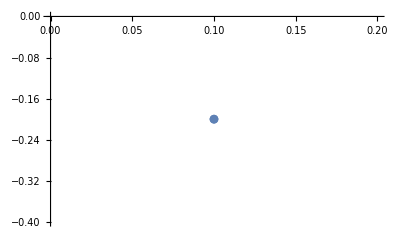
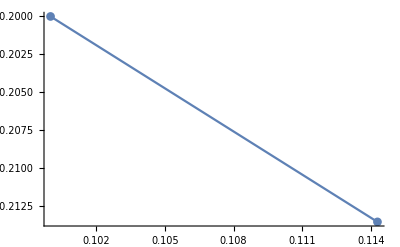
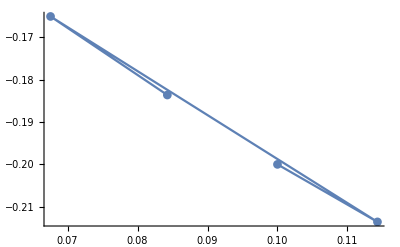
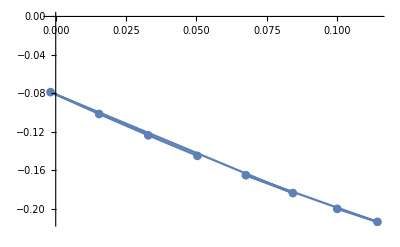

```mathematica
lAnimations=Table[ListPlot[fUnravel[test][[i]][[All,2]],Joined->True,PlotMarkers->Automatic,PlotRange->Automatic],{i,1,Length@test-1,1}]
```

```mathematica
ListAnimate[lAnimations]
```